# Approximate Quasisymmetry

## Input Parameters

```mathematica
R0=1;sigma0=0;NFP=3;
(*Number of Axis Fourier Coefficients*)
naxR=3;naxZ=naxR;
(*psi initial = psi31,psi32,psi33,psi34,sigma,F0*)
psiinit[t_]={0.01Cos[NFP t],0.01Sin[NFP t],0.01Cos[NFP t],0.01Sin[NFP t],0.01 Cos[NFP t],0.1};
```

## Axis Functions

```mathematica
R[x_]=R0+Sum[eR[n] Cos[n NFP x],{n,1,naxR}];
Z[x_]=Sum[eZ[n] Sin[n NFP x],{n,1,naxZ}];
closedCurve[x_]={R[x]Cos[x],R[x]Sin[x],Z[x]};
 curvFunc1[x_]=Chop[ComplexExpand[Norm[Cross[closedCurve'[x], closedCurve''[x]]]]/ComplexExpand[Norm[closedCurve'[x]]^3],10^-6];
torsFunc1[x_]=Chop[Dot[Cross[closedCurve'[x], closedCurve''[x]], closedCurve'''[x]]/ComplexExpand[Norm[Cross[closedCurve'[x], closedCurve''[x]]]]^2,10^-6];
sprimeFunc1[x_]=Chop[ComplexExpand[Norm[closedCurve'[x]]],10^-6]//Quiet;
```

```mathematica
optsComp={Table[eR[n]->er[[n]],{n,1,naxR}],Table[eZ[n]->ez[[n]],{n,1,naxZ}]}//Flatten//Quiet;
{curvFunc[phi_,er_,ez_],curvFuncp[phi_,er_,ez_],curvFuncpp[phi_,er_,ez_],curvFuncppp[phi_,er_,ez_]}={curvFunc1[phi],D[curvFunc1[phi],phi]/sprimeFunc1[phi],D[D[curvFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi],D[D[D[curvFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi]}/.optsComp//Quiet;
{torsFunc[phi_,er_,ez_],torsFuncp[phi_,er_,ez_],torsFuncpp[phi_,er_,ez_]}={torsFunc1[phi],D[torsFunc1[phi],phi]/sprimeFunc1[phi],D[D[torsFunc1[phi],phi]/sprimeFunc1[phi],phi] 1/sprimeFunc1[phi]}/.optsComp//Quiet;
sprimeFunc[phi_,er_,ez_]=sprimeFunc1[phi]/.optsComp//Quiet;
```

## Set of Equations

```mathematica
(*σ'[s]-sigmap[s]=0*)
sigmap[s_]=Flatten@(-(F0 ηb^4)/k[s]^4-F0 (1+σ[s]^2)-(2 ηb^2 α'[s])/k[s]^2);
(*psi'-psiMatA[s]psi[s]-psiMatB[s]=0*)
psiMatA[s_]=({{-3 F0 σ[s]+(2 k'[s])/k[s], (5 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+3 α'[s], (3 k'[s])/k[s], 3/2 ((F0 ηb^2)/k[s]^2+(F0 k[s]^2 (1+σ[s]^2))/ηb^2+2 α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], F0 σ[s]-(2 k'[s])/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(3 F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-3 α'[s], (3 k'[s])/k[s]}, {-F0 σ[s]+k'[s]/k[s], -(3 F0 ηb^2)/(2 k[s]^2)-(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)-α'[s], 0, 3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s])}, {(3 F0 ηb^2)/(2 k[s]^2)+(F0 k[s]^2 (1+σ[s]^2))/(2 ηb^2)+α'[s], -F0 σ[s]+k'[s]/k[s], -3 ((F0 k[s]^2 (1+ηb^4/k[s]^4+σ[s]^2))/(2 ηb^2)+α'[s]), 0}});
psiMatB[s_]=1/(B0 c0)Flatten@({{({{(B0 c0 (2 F0^2 k[s]^8 σ[s]^5 (3 F0 ηb^2-k[s]^2 α'[s])+2 F0 k[s]^4 σ[s]^3 (4 F0^2 ηb^6+2 k[s]^6 (ηb^2-F0 α'[s])+2 ηb^2 k[s]^2 (k'[s]^2+5 F0 ηb^2 α'[s])+ηb^2 k[s]^4 (5 F0^2-3 α'[s]^2)+ηb^2 k[s]^3 k''[s])+F0 k[s]^7 σ[s]^4 (k'[s] (-8 F0 ηb^2+2 k[s]^2 α'[s])+k[s]^3 α''[s])+k[s] (4 ηb^6 k'[s]^3+6 F0 ηb^8 k'[s] α'[s]-2 k[s]^8 k'[s] (ηb^2-F0 α'[s])+ηb^2 k[s]^4 k'[s] (ηb^4-4 k'[s]^2-8 F0 ηb^2 α'[s])+3 ηb^2 k[s]^5 k'[s] k''[s]+F0 k[s]^9 α''[s]-6 ηb^6 k[s]^3 α'[s] α''[s]+6 ηb^2 k[s]^7 α'[s] α''[s]-k[s] (3 ηb^6 k'[s] k''[s]+F0 ηb^8 α''[s])+ηb^6 k[s]^2 (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s])-ηb^2 k[s]^6 (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s]))-k[s]^5 σ[s]^2 (2 k[s]^4 k'[s] (ηb^2-2 F0 α'[s])+4 ηb^2 k'[s] (k'[s]^2+4 F0 ηb^2 α'[s])-2 F0 k[s]^5 α''[s]-6 ηb^2 k[s]^3 α'[s] α''[s]+k[s] (-3 ηb^2 k'[s] k''[s]+4 F0 ηb^4 α''[s])+ηb^2 k[s]^2 (2 k'[s] (5 F0^2-α'[s]^2)+Derivative[3][k][s]))+σ[s] (2 F0^3 ηb^10-2 F0 k[s]^10 (-2 ηb^2+F0 α'[s])+2 F0 ηb^6 k[s]^2 (4 k'[s]^2+7 F0 ηb^2 α'[s])+ηb^2 k[s]^8 (4 F0^3+3 ηb^2 α'[s]-6 F0 α'[s]^2)+2 k[s]^4 (-2 ηb^4 k'[s]^2 α'[s]+3 F0 ηb^6 (F0^2+3 α'[s]^2))-2 F0 ηb^6 k[s]^3 k''[s]+2 F0 ηb^2 k[s]^7 k''[s]+4 ηb^4 k[s]^5 (2 α'[s] k''[s]+k'[s] α''[s])+2 k[s]^6 (2 F0 ηb^2 k'[s]^2+ηb^4 (2 F0 ηb^2+8 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])))))/(2 ηb^4 k[s]^7)}})}, {({{(B0 c0 (4 F0^3 ηb^12+4 F0 ηb^8 k[s]^2 (3 k'[s]^2+4 F0 ηb^2 α'[s])-2 F0 k[s]^12 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^4 (6 F0^3 ηb^8 σ[s]^2-2 ηb^6 k'[s]^2 α'[s]+F0 ηb^8 (F0^2+7 α'[s]^2))+2 F0 k[s]^11 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s]^3 (2 F0 σ[s] k'[s]+k''[s])+2 ηb^2 k[s]^8 (-2 F0^3 ηb^2+2 F0^3 ηb^2 σ[s]^4-(ηb^4-2 k'[s]^2) α'[s]-8 F0 ηb^2 α'[s]^2+2 σ[s]^2 α'[s] (k'[s]^2-8 F0 ηb^2 α'[s])+12 ηb^2 σ[s] α'[s] α''[s])-4 k[s]^5 (4 ηb^4 σ[s] k'[s] (k'[s]^2+2 F0 ηb^2 α'[s])-ηb^6 (2 α'[s] k''[s]+k'[s] α''[s]))+2 ηb^2 k[s]^9 (8 F0 σ[s]^3 k'[s] α'[s]+σ[s] k'[s] (ηb^2+8 F0 α'[s])-2 (2 α'[s] k''[s]+k'[s] α''[s])-2 σ[s]^2 (2 α'[s] k''[s]+k'[s] α''[s]))-4 ηb^4 k[s]^7 (4 F0^2 σ[s]^3 k'[s]-F0 k''[s]-F0 σ[s]^2 k''[s]+σ[s] (2 k'[s] (F0^2-α'[s]^2)+Derivative[3][k][s]))-ηb^2 k[s]^10 (24 F0^2 σ[s]^4 α'[s]-8 F0 σ[s] α''[s]-8 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (3 F0 ηb^2+36 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))+ηb^4 k[s]^6 (4 F0 (-3+σ[s]^2) k'[s]^2+12 σ[s] k'[s] k''[s]+ηb^2 (-3 F0 ηb^2+4 F0^2 (-1+2 σ[s]^2) α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))))/(4 ηb^4 k[s]^9)}})}, {({{(B0 c0 (2 F0^3 ηb^10 σ[s]+2 F0 k[s]^9 (1+σ[s]^2)^2 k'[s] α'[s]-ηb^2 k[s]^5 k'[s] (ηb^4+4 (1+σ[s]^2) k'[s]^2+4 F0 ηb^2 (1+σ[s]^2) α'[s])-2 k[s] (2 ηb^6 k'[s]^3+3 F0 ηb^8 k'[s] α'[s])+ηb^6 k[s]^2 (2 F0 σ[s] (2 k'[s]^2+F0 ηb^2 α'[s])+3 k'[s] k''[s]+F0 ηb^2 α''[s])+F0 k[s]^10 (1+σ[s]^2) (-2 F0 σ[s]^3 α'[s]+σ[s] (ηb^2-2 F0 α'[s])+α''[s]+σ[s]^2 α''[s])+2 ηb^6 k[s]^4 (2 F0^3 σ[s]^3+2 σ[s] (F0^3-F0 α'[s]^2)+3 α'[s] α''[s])+ηb^2 k[s]^8 (2 F0^3 σ[s]^5+σ[s] (2 F0^3+ηb^2 α'[s]-4 F0 α'[s]^2)+4 σ[s]^3 (F0^3-F0 α'[s]^2)+6 α'[s] α''[s]+6 σ[s]^2 α'[s] α''[s])+ηb^2 k[s]^6 (4 F0 σ[s]^3 k'[s]^2+2 F0 σ[s] (ηb^4+2 k'[s]^2)+3 k'[s] k''[s]+2 F0 ηb^2 α''[s]+σ[s]^2 (3 k'[s] k''[s]+2 F0 ηb^2 α''[s]))-ηb^6 k[s]^3 (2 k'[s] (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+Derivative[3][k][s])-ηb^2 k[s]^7 (1+σ[s]^2) (2 k'[s] (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+Derivative[3][k][s])))/(2 ηb^4 k[s]^7)}})}, {({{-(B0 c0 (4 F0^3 ηb^12+k[s]^2 (-8 F0^2 ηb^4 k[s]^5 σ[s] (1+σ[s]^2) k'[s]+4 F0 ηb^8 (3 k'[s]^2+4 F0 ηb^2 α'[s])+2 F0 k[s]^10 (1+σ[s]^2)^2 (F0^2+2 F0^2 σ[s]^2-α'[s]^2)+2 k[s]^2 (F0^3 ηb^8 (5+6 σ[s]^2)-2 ηb^6 k'[s]^2 α'[s]+7 F0 ηb^8 α'[s]^2)+2 ηb^2 k[s]^6 (2 F0^3 ηb^2 (2+5 σ[s]^2+3 σ[s]^4)+(ηb^4-2 (1+σ[s]^2) k'[s]^2) α'[s]+6 F0 ηb^2 (1+σ[s]^2) α'[s]^2)-2 F0 k[s]^9 (1+σ[s]^2)^2 (2 F0 σ[s] k'[s]-k''[s])-2 F0 ηb^8 k[s] (2 F0 σ[s] k'[s]+k''[s])+4 ηb^6 k[s]^3 (2 α'[s] (-F0 σ[s] k'[s]+k''[s])+k'[s] α''[s])+2 ηb^2 k[s]^7 (ηb^2 σ[s] k'[s]-4 F0 σ[s] k'[s] α'[s]-4 F0 σ[s]^3 k'[s] α'[s]+4 α'[s] k''[s]+4 σ[s]^2 α'[s] k''[s]+2 (1+σ[s]^2) k'[s] α''[s])+ηb^2 k[s]^8 (16 F0^2 σ[s]^4 α'[s]-4 F0 σ[s] α''[s]-4 F0 σ[s]^3 α''[s]+2 (F0 ηb^2+6 F0^2 α'[s]-2 α'[s]^3+Derivative[3][α][s])+σ[s]^2 (F0 ηb^2+28 F0^2 α'[s]-4 α'[s]^3+2 Derivative[3][α][s]))+ηb^4 k[s]^4 (12 F0 (1+σ[s]^2) k'[s]^2+ηb^2 (3 F0 ηb^2+4 F0^2 (7+8 σ[s]^2) α'[s]-4 α'[s]^3-4 F0 σ[s] α''[s]+2 Derivative[3][α][s])))))/(4 ηb^4 k[s]^9)}})}});
(*psi2[s]-psi32[s]=0*)
psi32[s_]=1/(B0 c0)1/(4 F0 ηb^2 k[s]^6)B0 c0 (4 F0^3 ηb^6 k[s] σ[s]+4 F0^2 ηb^6 k'[s]-2 k[s]^6 k'[s] (ηb^2+2 F0 (1+σ[s]^2) α'[s])+4 k[s]^2 (2 ηb^2 k'[s]^3+F0 ηb^4 k'[s] α'[s])-4 F0 ηb^2 k[s]^4 (F0 (1+σ[s]^2) k'[s]-σ[s] k''[s])+2 ηb^2 k[s]^3 (2 F0 σ[s] (-k'[s]^2+3 F0 ηb^2 α'[s])-4 k'[s] k''[s]-3 F0 ηb^2 α''[s])+F0 k[s]^7 (ηb^2 σ[s]+4 F0 (σ[s]+σ[s]^3) α'[s]-2 (1+σ[s]^2) α''[s])+4 ηb^2 k[s]^5 (F0^3 (σ[s]+σ[s]^3)+2 F0 σ[s] α'[s]^2-2 α'[s] α''[s]));
```

## Compiled Functions

```mathematica
erT=Table[eR[i],{i,1,naxR}];ezT=Table[eZ[i],{i,1,naxZ}];
opts1={k[phi]->curvFunc[phi,er,ez],k'[phi]->curvFuncp[phi,er,ez],k''[phi]->curvFuncpp[phi,er,ez],k'''[phi]->curvFuncppp[phi,er,ez],α'[phi]->torsFunc[phi,er,ez],α''[phi]->torsFuncp[phi,er,ez],α'''[phi]->torsFuncpp[phi,er,ez],σ[phi]->psi[5],F0->psi[6],ηb->etabb}//Quiet;
optsCT3={Table[psi[i]->psii[[i]],{i,1,6}],etabb->etabbb}//Quiet//Flatten;
fpsi3=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[(-sprimeFunc[phi,er,ez](psiMatA[phi].{psi[1],psi[2],psi[3],psi[4]}+psiMatB[phi]))/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
fsigma=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[(-sprimeFunc[phi,er,ez]sigmap[phi])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
dfpsi3=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[-sprimeFunc[phi,er,ez](psiMatA[phi])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
dfsigma=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[-sprimeFunc[phi,er,ez](D[sigmap[phi],σ[phi]])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
dfdF0=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[-sprimeFunc[phi,er,ez](D[sigmap[phi],F0])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
fpsi2=Compile[{{phi,_Real},{er,_Real,1},{ez,_Real,1},{psii,_Real,1},{etabbb,_Real}},Evaluate[(psi[2]-psi32[phi])/.opts1/.optsCT3],CompilationTarget->"C",Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"]//Quiet;
```

## Residual and Jacobian Matrices

## Sigma

```mathematica
Clear[qsresidualsigma];
qsresidualsigma[Dmat_,psii_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{delta=(2 π)/ns },
fsigmaMat=Table[fsigma[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
dfsigmaMat=Table[dfsigma[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
dfdF0Mat=Table[dfdF0[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
f1Mat={
Dmat.psii[[All,5]]+fsigmaMat[[All]],
psii[[ns,5]]-sigma0
}//Flatten;
myArrayFlatten=Flatten/@Flatten[#,{{1,3}}]&;
Jacf1Mat=myArrayFlatten@{
{Dmat+DiagonalMatrix[dfsigmaMat],dfdF0Mat}
};
Jacf1Mat=Append[Jacf1Mat,{ConstantArray[0, ns-1],1,0}//Flatten];
{f1Mat,Jacf1Mat}
];
solveSigma[Dmat_,nIts_,tol_,nLineS_,psiA_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{deltaold=0,delta=(2 π)/ns },
psii=psiA;
For[i=1,i≤nIts,i++,
{f1,Jacf1}=qsresidualsigma[Dmat,psii,er,ez,etab,ns,sigma0];
deltay=-LinearSolve[Jacf1,f1]//Quiet;
res[i]=Norm[deltay];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
psiAtemp=psii;psiAtemp[[All,5]]=psiAtemp[[All,5]]+deltay[[1;;ns]];psiAtemp[[All,6]]=psiAtemp[[All,6]]+deltay[[ns+1]];
{f2,Jacf2}=qsresidualsigma[Dmat,psiAtemp,er,ez,etab,ns,sigma0];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2];
];
psii=psiAtemp;
deltaold=deltay;
];
psii
]
```

## Psi3

```mathematica
Clear[qsresidualpsi3];
qsresidualpsi3[Dmat_,psii_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{delta=(2 π)/ns },
fpsi3Mat=Table[fpsi3[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
dfpsi3Mat=Table[dfpsi3[delta i,er,ez,psii[[i]],etab],{i,1,ns}];
f1Mat={
Dmat.psii[[All,1]]+fpsi3Mat[[All,1]],
Dmat.psii[[All,2]]+fpsi3Mat[[All,2]],
Dmat.psii[[All,3]]+fpsi3Mat[[All,3]],
Dmat.psii[[All,4]]+fpsi3Mat[[All,4]]
}//Flatten;
zeroarray=DiagonalMatrix[ConstantArray[0,ns]];
myArrayFlatten=Flatten/@Flatten[#,{{1,3}}]&;
Jacf1Mat=myArrayFlatten@{
{Dmat+DiagonalMatrix[dfpsi3Mat[[All,1,1]]],DiagonalMatrix[dfpsi3Mat[[All,1,2]]],DiagonalMatrix[dfpsi3Mat[[All,1,3]]],DiagonalMatrix[dfpsi3Mat[[All,1,4]]]},
{DiagonalMatrix[dfpsi3Mat[[All,2,1]]],Dmat+DiagonalMatrix[dfpsi3Mat[[All,2,2]]],DiagonalMatrix[dfpsi3Mat[[All,2,3]]],DiagonalMatrix[dfpsi3Mat[[All,2,4]]]},
{DiagonalMatrix[dfpsi3Mat[[All,3,1]]],DiagonalMatrix[dfpsi3Mat[[All,3,2]]],Dmat+DiagonalMatrix[dfpsi3Mat[[All,3,3]]],DiagonalMatrix[dfpsi3Mat[[All,3,4]]]},
{DiagonalMatrix[dfpsi3Mat[[All,4,1]]],DiagonalMatrix[dfpsi3Mat[[All,4,2]]],DiagonalMatrix[dfpsi3Mat[[All,4,3]]],Dmat+DiagonalMatrix[dfpsi3Mat[[All,4,4]]]}
};
{f1Mat,Jacf1Mat}
];
solvepsi3[Dmat_,nIts_,tol_,nLineS_,psiA_,er_,ez_,etab_,ns_,sigma0_]:=Module[
{deltaold=0,delta=(2 π)/ns },
psii=psiA;
For[i=1,i≤nIts,i++,
{f1,Jacf1}=qsresidualpsi3[Dmat,psii,er,ez,etab,ns,sigma0];
deltay=-LinearSolve[Jacf1,f1]//Quiet;
res[i]=Norm[deltay];
If[(Abs[Norm[deltay]-Norm[deltaold]])/√ns<tol,Break[]];
For[j=1,j<nLineS,j++,
psiAtemp=psii;psiAtemp[[All,1]]=psiAtemp[[All,1]]+deltay[[1;;ns]];psiAtemp[[All,2]]=psiAtemp[[All,2]]+deltay[[ns+1;;2ns]];
psiAtemp[[All,3]]=psiAtemp[[All,3]]+deltay[[2ns+1;;3ns]];psiAtemp[[All,4]]=psiAtemp[[All,4]]+deltay[[3ns+1;;4ns]];
{f2,Jacf2}=qsresidualpsi3[Dmat,psiAtemp,er,ez,etab,ns,sigma0];
If[Abs[Norm[f2]]<Abs[Norm[f1]],Break[],deltay=deltay/2];
];
psii=psiAtemp;
deltaold=deltay;
];
psii
]
```

## Objective Function

```mathematica
Clear[objFuncpsi3];
objFuncpsi3[etab_,er0_,ez0_,nIts_,tol_,nLineS_,psiinit_,ns_,sigma0_]:=
Module[{delta=(2 Pi)/ns},
psii=Table[psiinit[delta i],{i,1,ns}];
(*Derivative Matrix*)
column1=Prepend[ Table[ 0.5 (-1)^n Cot[n/2 delta],{n,1,ns-1}],0];
column2=RotateRight[Reverse[column1]];
Dmat=ToeplitzMatrix[column1,column2];
(*Solve Sigma*)
psisol1=solveSigma[Dmat,nIts,tol,nLineS,psii,er0,ez0,etab,ns,sigma0];
(*Solve Psi3*)
psisol2=solvepsi3[Dmat,nIts,tol,nLineS,psisol1,er0,ez0,etab,ns,sigma0];
(*psi2 Constraint*)
residpsi2=Table[fpsi2[delta i,er0,ez0,psisol2[[i]],etab],{i,1,ns}];
{Norm[residpsi2]+Norm[psisol2[[All,1;;4]]],psisol2,residpsi2}
];
```

## Optimization

```mathematica
ns=100;nIts=16;nLineS=3;maxiterations=3000;tol=10^-6;
etabmin=0.4;etabmax=1.2;eR1min=0.1;eR1max=0.2;eZ1min=-eR1max;eZ1max=-eR1min;eR2min=-0.02;eR2max=0.02;eZ2min=eR2min;eZ2max=eR2max;eR3min=-0.01;eR3max=0.01;eZ3min=eR3min;eZ3max=eR3max;
varstemp={};OutputFile="/Users/rogeriojorge/Dropbox/senac/quasisymmetry/HighOrderQSmath.txt";
Export[OutputFile,"etab, eR1, eR2, eR3, eZ1, eZ2, eZ3\n"];ii=0;
(*Dynamic@If[Length@varstemp>3,ListPlot[Transpose@varstemp,PlotRange->{Automatic,{-0.2,0.2}},GridLines->{{Length@varstemp},{}},PlotLegends->{OverBar["η"]/8,"eR_1","10 eR_2","10 eR_3","eZ_1","10 eZ_2","10 eZ_3"},ImageSize->1100,PlotStyle->{PointSize[.005]}]]*)
{etabsol,eRsol,eZsol}={etabb,{eR1,eR2,eR3},{eZ1,eZ2,eZ3}}/.NMinimize[
{Hold[objFuncpsi3[etabb,{eR1,eR2,eR3},{eZ1,eZ2,eZ3},nIts,tol,nLineS,psiinit,ns,sigma0][[1]]],etabmin<etabb<etabmax&&eR1min<eR1<eR1max&&eZ1min<eZ1<eZ1max&&eR2min<eR2<eR2max&&eZ2min<eZ2<eZ2max&&eR3min<eR3<eR3max&&eZ3min<eZ3<eZ3max},
{{etabb,etabmin,etabmax},{eR1,eR1min,eR1max},{eZ1,eZ1min,eZ1max},{eR2,eR2min,eR2max},{eZ2,eZ2min,eZ2max},{eR3,eR3min,eR3max},{eZ3,eZ3min,eZ3max}},
AccuracyGoal->4,PrecisionGoal->4,WorkingPrecision->10,MaxIterations->maxiterations(*,Method->{"DifferentialEvolution","ScalingFactor"->5}*)
,(*EvaluationMonitor:>AppendTo[varstemp,{etabb/8,eR1,10  eR2,10 eR3, eZ1,10eZ2,10eZ3}],*)
StepMonitor:>{ii++,PutAppend["Iteration "<>ToString@ii<>" -> "<>ToString@etabb<>", "<>ToString@eR1<>", "<>ToString@eR2<>", "<>ToString@eR3<>", "<>ToString@eZ1<>", "<>ToString@eZ2<>", "<>ToString@eZ3,OutputFile];{etabsol,eRsol,eZsol}={etabb,{eR1,eR2,eR3},{eZ1,eZ2,eZ3}}}
][[2]];
PutAppend["Solution with objective function = "<>ToString@(objFuncpsi3[etabsol,eRsol,eZsol,nIts,tol,nLineS,psiinit,ns,sigma0][[1]])<>" -> "<>ToString@etabsol<>", "<>ToString@eRsol<>", "<>ToString@eZsol,OutputFile];
```

```mathematica
etabsol
eRsol
eZsol
```

1.15584

{0.19974,0.0144556,0.000138757}

{-0.199986,-0.0198478,-0.000742938}

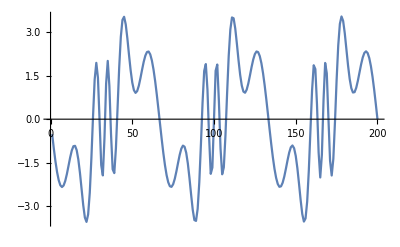

```mathematica
solfin=objFuncpsi3[etabsol,eRsol,eZsol,30,10^-11,10,psiinit,200,sigma0];
ListLinePlot[solfin[[2,All,2]],PlotRange->All]
```

## Particular Solution

```mathematica
(*
etab=0.7;ns=150;nIts=20;tol=10^-5;nLineS=8;
er0={0.04,0.01};ez0={0.04,0.02};
solpart=objFuncpsi3[etab,er0,ez0,nIts,tol,nLineS,psiinit,ns,sigma0];
ListLinePlot[solfin[[2,All,1]]]
*)
```